```mathematica
(* Program - Mars
Date: Oct 3, 2026
Purpose: To plot the distance between Earth and Mars after an encounter with a primordial black hole 
Usage: Pick mu = mass of the black hole in kg; vb = speed of black hole. The fiducial values of these parameters are 10^18 kg and 200 km/sec respectively. Also pick (xzero, yzero) = the Cartesian coordinates in au of the black hole when it passes the ecliptic plane; (alpha, beta) = the co-latitude and longitude of the black hole velocity vector in radians *)
```

```mathematica
(* The next few commands specify the orbit unperturbed circular orbits of Earth and Mars *)
```

```mathematica
wearth = 2*Pi; phaseearth = (100.5*Pi)/180; aearth = 1.0;
```

```mathematica
xearth[ t_ ] := aearth*Cos[ wearth*t + phaseearth];
```

```mathematica
yearth[ t_ ] := aearth*Sin[ wearth*t + phaseearth ];
```

```mathematica
amars = 1.5237; wmars = (2*Pi)/(amars^(3/2)); phasemars = (-4.57*Pi)/180;
```

```mathematica
xmars[ t_ ]:= amars*Cos[ wmars*t+phasemars];
```

```mathematica
ymars[ t_ ] := amars*Sin[wmars*t+phasemars];
```

```mathematica
(* The time dependent tangents to the orbits are now specified. This is denoted hat{theta}_p(t) in the notes *)
```

```mathematica
txearth[ t_ ] := - Sin[ wearth*t+ phaseearth];
```

```mathematica
tyearth[ t_ ] := Cos[ wearth*t + phaseearth];
```

```mathematica
txmars[ t_ ]:= - Sin[ wmars*t+phasemars];
```

```mathematica
tymars[ t_ ]:= Cos[ wmars*t+phasemars];
```

```mathematica
(* The parameters for the black hole are specified. The speed is converted to astronomical units per year and is taken to be the fiducial value chosen by Tran et al. The values of alpha, beta, tzero, xzero and yzero must be assigned by the user. The Tran et al values are alpha = Pi-(2/450); beta = 0; xzero = 2; yzero = 0; tzero is not known *)
```

```mathematica
vb = (200000*365.25*24*60*60)/(1.496*(10^(11)));
```

```mathematica
alpha = 0; beta = 0;tzero=0;
```

```mathematica
vbx = vb*Sin[alpha]*Cos[beta];
vby = vb*Sin[alpha]*Sin[beta]; vbz=vb*Cos[alpha];
```

```mathematica
xzero = 1.5; yzero = -0.3;
```

```mathematica
(* Calculation of the tangential impulse. impulseearth here represents the quantity denotes I_theta / m in the notes; hence it has units of velocity in au per year. prefactorearth represents 2 G mu / 1 au which is equal to 4 Pi (mu / msun) *)
```

```mathematica
mu = 10^(18) ; msun = 2*(10^(30));
```

```mathematica
rminsquareearth = ((xearth[tzero]-xzero)^2) + ((yearth[tzero]-yzero)^2)- (( (xearth[tzero]-xzero)*(vbx/vb) + (yearth[tzero]-yzero)*(vby/vb) )^2);
```

```mathematica
numfirstearth = xzero*txearth[tzero]+yzero*tyearth[tzero];
```

```mathematica
numsecondearth=((vbx/vb)*txearth[tzero]+(vby/vb)*tyearth[tzero])*( (xearth[tzero]-xzero)*(vbx/vb)+(yearth[tzero]-yzero)*(vby/vb) );
```

```mathematica
numeearth = numfirstearth+numsecondearth;
```

```mathematica
prefactearth= (4*Pi*(mu/msun))/vb ;
```

```mathematica
impulseearth= (prefactearth*numeearth)/rminsquareearth
```

-4.72472×10^-14

```mathematica
rminsquaremars = ((xmars[tzero]-xzero)^2) + ((ymars[tzero]-yzero)^2)- (( (xmars[tzero]-xzero)*(vbx/vb) + (ymars[tzero]-yzero)*(vby/vb) )^2);
```

```mathematica
numfirstmars = xzero*txmars[tzero]+yzero*tymars[tzero];
```

```mathematica
numsecondmars=((vbx/vb)*txmars[tzero]+(vby/vb)*tymars[tzero])*( (xmars[tzero]-xzero)*(vbx/vb)+(ymars[tzero]-yzero)*(vby/vb) );
```

```mathematica
numemars = numfirstmars+numsecondmars;
```

```mathematica
prefactmars= (4*Pi*(mu/msun))/vb;
```

```mathematica
impulsemars= (prefactmars*numemars)/rminsquaremars
```

-8.29006×10^-13

```mathematica
(* In this section the displacements of Earth and Mars are computed *)
```

```mathematica
deltaxearth[ t_ ] := - 3*impulseearth*(t-tzero)*txearth[t]*HeavisideTheta[t-tzero];
```

```mathematica
deltayearth[ t_ ]:= - 3*impulseearth*(t-tzero)*tyearth[t]*HeavisideTheta[t-tzero];
```

```mathematica
deltaxmars[ t_ ]:= - 3*impulsemars*(t-tzero)*txmars[t]*HeavisideTheta[t-tzero];
```

```mathematica
deltaymars[ t_ ]:= - 3*impulsemars*(t-tzero)*tymars[t]*HeavisideTheta[t-tzero];
```

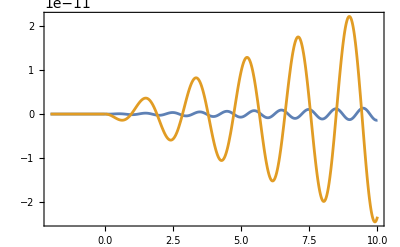

```mathematica
Plot[{deltaxearth[t], deltaxmars[t]},{t,-2, 10}, Frame -> True, PlotRange -> All]
```

```mathematica
(* This final segment calculates the change in distance between Earth and Mars *)
```

```mathematica
distearthmars[t_] := Sqrt[(xearth[t]-xmars[t])^2 + (yearth[t]-ymars[t])^2];
```

```mathematica
nearthmarsx[t_]:= (xearth[t]-xmars[t])/distearthmars[t];
```

```mathematica
nearthmarsy[t_]:= (yearth[t]-ymars[t])/distearthmars[t];
```

```mathematica
autom=1.496*(10^11);
```

```mathematica
deltaearthmars[t_]:=autom* (((deltaxearth[t]-deltaxmars[t])*nearthmarsx[t])+ ((deltayearth[t]-deltaymars[t])*nearthmarsy[t]));
```

```mathematica
tranestimate[t_]:=autom*prefactmars*(t-tzero)*HeavisideTheta[t-tzero]/Sqrt[rminsquaremars];
```

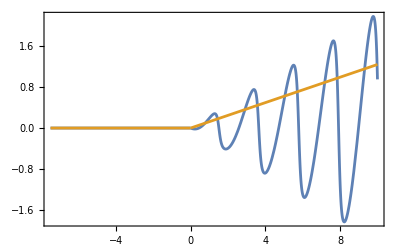

```mathematica
Plot[{deltaearthmars[t],tranestimate[t]},{t,tzero-7.5,tzero+ 10.}, Frame -> True, PlotRange -> All]
```

```mathematica
Export[ "marsplot.jpg", %41,"JPG", ImageResolution -> 300]
```

marsplot.jpg

```mathematica
(*Monte Carlo sim for PHB flyby params that are within detection window?*)
```

```mathematica
(*----------Cell 1:physics functions, ----------*)msun=1.98847*^30; (*kg*)
gmsun=4 Pi^2; (*au^3/yr^2*)
mcSunKick=True; (*subtract the Sun's kick from each planet's kick*)
mcFloor=10.^-8; (*floor on d.d so a near collision does not blow up the 1/d^2 kick,au^2*)
(*{a,omega,phase at t=0} per planet*)
mcPlanets=<|"Earth"->{aearth,wearth,phaseearth},"Mars"->{amars,wmars,phasemars}|>;
mcXY[name_,t_]:=Module[{a,w,ph},{a,w,ph}=mcPlanets[name];
{a Cos[w t+ph],a Sin[w t+ph]}];
(*velocity kick (au/yr) on a body at R;
bvec is perpendicular to vhat;
mus=mu/msun*)
mcKick[R_,bvec_,vhat_,mus_]:=Module[{d},d=bvec-(R-(R.vhat) vhat);
(2 gmsun mus/vb) d/Max[d.d,mcFloor]];
(*displacement of one planet from its unperturbed orbit,in au.ev={vhat,bvec,tca};
tca=time the BH is at b.each planet feels the kick when the BH is closest to that planet,at time ti,found by iterating ti=tca+(R.vhat)/vb.the kick is split into radial (ur) and tangential (ut) parts and the epicycle response (eqs 57-58 of the impulse response notes) gives xi and eta.the-3 ut tau term in eta is the secular piece*)
mcDisp[name_,{vhat_,bvec_,tca_},mus_,tg_]:=Module[{a,w,ph,ti,R,u,rh,th,ur,ut,tau,xi,eta,ang},{a,w,ph}=mcPlanets[name];
ti=tca;
Do[R=a {Cos[w ti+ph],Sin[w ti+ph],0.};
ti=tca+(R.vhat)/vb,{2}];
R=a {Cos[w ti+ph],Sin[w ti+ph],0.};
u=mcKick[R,bvec,vhat,mus]-If[mcSunKick,mcKick[{0.,0.,0.},bvec,vhat,mus],0.];
rh={Cos[w ti+ph],Sin[w ti+ph],0.};
th={-Sin[w ti+ph],Cos[w ti+ph],0.};
ur=u.rh;ut=u.th;
tau=UnitStep[tg-ti] (tg-ti);
xi=(ur/w) Sin[w tau]+(2 ut/w) (1-Cos[w tau]);
eta=(2 ur/w) (Cos[w tau]-1)+(4 ut/w) Sin[w tau]-3 ut tau;
ang=w tg+ph;
{xi Cos[ang]-eta Sin[ang],xi Sin[ang]+eta Cos[ang]}];
(*secular only version from the notes,planet held at its position at tca.used below to check mcDisp*)
mcDispSecular[name_,{vhat_,bvec_,tca_},mus_,tg_]:=Module[{a,w,ph,R,u,th0,ut,tau},{a,w,ph}=mcPlanets[name];
R=a {Cos[w tca+ph],Sin[w tca+ph],0.};
u=mcKick[R,bvec,vhat,mus]-If[mcSunKick,mcKick[{0.,0.,0.},bvec,vhat,mus],0.];
th0={-Sin[w tca+ph],Cos[w tca+ph],0.};
ut=u.th0;tau=UnitStep[tg-tca] (tg-tca);
{3 ut tau Sin[w tg+ph],-3 ut tau Cos[w tg+ph]}];
(*Earth-partner distance residual in metres,as a list over tg.last argument picks the displacement model*)
mcDeltaR[partner_,ev_,mus_,tg_,disp_:mcDisp]:=Module[{dE,dX,xe,ye,xp,yp,d},dE=disp["Earth",ev,mus,tg];
dX=disp[partner,ev,mus,tg];
{xe,ye}=mcXY["Earth",tg];{xp,yp}=mcXY[partner,tg];
d=Sqrt[(xe-xp)^2+(ye-yp)^2];
autom ((xe-xp) (dE[[1]]-dX[[1]])+(ye-yp) (dE[[2]]-dX[[2]]))/d];
```

```mathematica
(*----------Cell 2:turns vbx,vby,vbz,xzero,yzero,tzero into vhat,bvec,tca (when the BH is closest to the Sun)----------*)mcEvNotebook=Module[{vh,P0,bv,tc},vh=N[{vbx,vby,vbz}/vb];
(*unit vector along the BH velocity*)P0=N[{xzero,yzero,0}];
(*point where the BH crosses the ecliptic*)bv=P0-(P0.vh) vh;
(*impact vector:Sun to closest point on the path*)tc=tzero-(P0.vh)/vb;
(*time of closest approach*){vh,bv,tc}];
(*Time grid:2 yr before tzero to 10 yr after,every 10 days*)
tgB=Range[tzero-2+0.0013,tzero+10,10/365.25];
mus0=mu/msun; (*BH mass in solar masses*)
(*Earth-Mars distance change in metres,should be flat before t_0*)
dMars=mcDeltaR["Mars",mcEvNotebook,mus0,tgB];
```

{0.,13.765,1.01156}

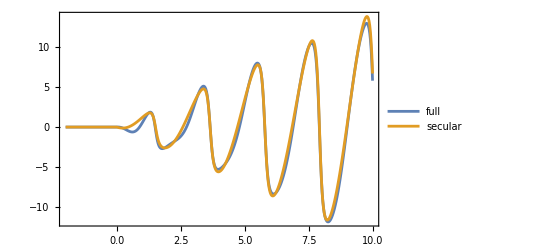

```mathematica
(*----------Cell 2b:check of the full response against the secular formula,Sun's kick off so both use the same physics.the two should agree to roughly 10% at late times and the full one should be exactly 0 before the kick----------*)mcSunKick=False;
dFull=mcDeltaR["Mars",mcEvNotebook,mus0,tgB];
dSec=mcDeltaR["Mars",mcEvNotebook,mus0,tgB,mcDispSecular];
mcSunKick=True;
{Max[Abs[Pick[dFull,Thread[tgB<tzero]]]],Max[Abs[dSec]],Max[Abs[dFull-dSec]]}
ListLinePlot[{Transpose[{tgB,dFull}],Transpose[{tgB,dSec}]},Frame->True,PlotLegends->{"full","secular"}]


(*----------Cell 3:sampling random flybys----------*)mcSample[bmax_,t0_,Tobs_]:=Module[{c,ph,v,h,e1,e2,b,psi,bv},(*isotropic direction*)c=RandomReal[{-1,1}];
ph=RandomReal[{0,2 Pi}];
v={Sqrt[1-c^2] Cos[ph],Sqrt[1-c^2] Sin[ph],c};
(*two unit vectors perpendicular to v*)h=If[Abs[c]<0.9,{0.,0.,1.},{1.,0.,0.}];
e1=Normalize[Cross[v,h]];e2=Cross[v,e1];
(*impact vector,uniform over a disk of radius bmax*)b=bmax Sqrt[RandomReal[]];
psi=RandomReal[{0,2 Pi}];
bv=b (Cos[psi] e1+Sin[psi] e2);
{v,bv,RandomReal[{t0,t0+Tobs}]}];
mcBmax=50.; (*au,radius of the target disk (as in Tran et al.)*)
mcT0=0.; (*start of the window,yr*)
mcTobs=26.; (*length of the window,yr*)
mcN=200000; (*number of events,20 000 took a few seconds so this should take a minute or two*)
SeedRandom[1];
mcEvents=Table[mcSample[mcBmax,mcT0,mcTobs],{mcN}];
```

```mathematica
(*sampling sanity check here*)
{Length[mcEvents],Max[Norm/@mcEvents[[All,2]]],(*just under 50*)Mean[mcEvents[[All,1,3]]],(*near 0*)Max[Abs[(Dot@@#)&/@mcEvents[[All,{1,2}]]]]} (* ~0:bvec perp vhat*)


(*----------Cell 4a:Imagine you measure the Earth-Mars distance every 40 days for 26 years,but your ruler is only accurate to 0.1 m.Now a black hole flyby happens and gives Mars a tiny nudge.The Earth-Mars distance starts to wobble slightly.Is the wobble big enough to notice above your ruler's fuzziness?q is the biggest wobble divided by 0.1 m----------*)mcTg=Range[mcT0,mcT0+mcTobs,40/365.25];
(*list of measurement dates:day 0,day 40,day 80,and so on up to 26 years*)
mcTargets=<|"Mars"->0.1|>;
(*sigma_r in metres,"Earth to Mars, accurate to 0.1 m"*)
mcMuBase=10.^18; (*kg=1e21 g*)
mcQ[ev_,mus_]:=Sqrt[Max[Total[(mcDeltaR[#,ev,mus,mcTg]/mcTargets[#])^2&/@Keys[mcTargets]]]];
mcQfor[events_,mus_]:=Table[mcQ[ev,mus],{ev,events}];
```

{200000,49.9999,-0.00168204,1.07275×10^-14}

```mathematica
(*----------Cell 4b:all events----------*)AbsoluteTiming[mcQ1=mcQfor[mcEvents,mcMuBase/msun];]
{Min[mcQ1],Median[mcQ1],Max[mcQ1]}
```

{66.0196,Null}

{0.,0.0138285,591.519}

```mathematica
(*----------Cell 5a:ingredients for the rate----------*)mcGeVkg=1.78266*^-27; (*kg per GeV/c^2*)
mcAuCm=autom*100.; (*cm per au,from autom=1.496e11 m*)
mcRhoDM=0.4 mcGeVkg mcAuCm^3; (*local DM density,kg/au^3*)
mcSigma=Pi mcBmax^2; (*target cross section,au^2*)
(*flyby rate through the target disk,per year;vb is already in au/yr*)
mcFlybyRate[Mkg_]:=(mcRhoDM/Mkg) mcSigma vb;
(*number of the events that are detectable at mass Mkg for threshold q0;uses the linear rescaling q(M)=q_base*Mkg/mcMuBase*)
mcCount[q_,Mkg_,q0_]:=Total[UnitStep[q-q0 mcMuBase/Mkg]];
(*sanity checks: ~1.4e0 PBHs inside 5.2 au at 1e18 g,and rate at 1e21 g*)
{mcRhoDM (4/3) Pi 5.2^3/(10^15),mcFlybyRate[10.^18],mcFlybyRate[10.^18] mcTobs}
```

{1.40612,0.791071,20.5678}

```mathematica
(*----------Cell 5b:scan mass and q0----------*)mcQ0List={1,10^-2,10^-3,10^-4}; (*q0=1 conservative;others are the paper's benchmark range*)
mcMg=10^Range[12.,25.,0.1]; (*PBH mass grid in grams*)
mcMinValidG=10.^18; (*Tran et al:the method breaks down below this because the flybys overlap*)
mcMinCount=10; (*a window edge needs at least this many events behind it*)
(*each row:{M[g],p,error on p,events above threshold,detectable rate[1/yr],expected N in window,valid mass?}*)
mcRowsFor[q_,q0_]:=Table[Module[{Mkg=Mg/1000.,n=Length[q],c,p,G},c=mcCount[q,Mkg,q0];p=c/n;G=mcFlybyRate[Mkg];
{Mg,p,Sqrt[p (1-p)/n],c,G p,G p mcTobs,Mg>=mcMinValidG}],{Mg,mcMg}];
mcScan=AssociationMap[mcRowsFor[mcQ1,#]&,mcQ0List];
```

q0 | window for N_det >= 1 [g] | peak-rate mass [g]
1 | None | 6.30957×10^19
1/100 | {1.×10^18,1.58489×10^22} | 6.30957×10^17
1/1000 | {1.×10^18,1.99526×10^22} | 6.30957×10^16
1/10000 | {1.×10^18,1.99526×10^22} | 6.30957×10^15

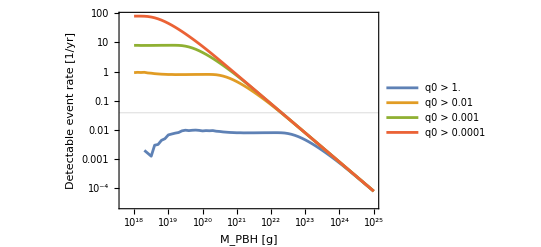

```mathematica
(*----------Cell 5c:results----------*)(*mass range (grams) with expected N_det>=1 in the observing window,only for valid masses and edges with enough events*)mcWindow[rows_]:=With[{ok=Select[rows,#[[6]]>=1&&#[[7]]&&#[[4]]>=mcMinCount&]},If[ok==={},None,{Min[ok[[All,1]]],Max[ok[[All,1]]]}]];
(*mass at which the detectable rate peaks,compare 2.3e18 g*q0 from Tran eq 20*)
mcPeak[rows_]:=First[MaximalBy[rows,#[[5]]&]][[1]];
Grid[Prepend[Table[{q0,mcWindow[mcScan[q0]],mcPeak[mcScan[q0]]},{q0,mcQ0List}],{"q0","window for N_det >= 1 [g]","peak-rate mass [g]"}],Frame->All]
(*analogue of Fig.5,valid masses only*)
ListLogLogPlot[Table[Select[{#[[1]],#[[5]]}&/@Select[mcScan[q0],#[[7]]&],#[[2]]>0&],{q0,mcQ0List}],Joined->True,Frame->True,Axes->False,FrameLabel->{"M_PBH [g]","Detectable event rate [1/yr]"},GridLines->{None,{1/mcTobs}},(*N_det=1 over the window*)PlotLegends->Table[Row[{"q0 > ",N[q0]}],{q0,mcQ0List}]]
```

```mathematica
mcMmaxG=mcRhoDM mcSigma vb mcTobs*1000. (*grams;expect~2e22 g*)
```

2.05678×10^22

```mathematica
(*----------Cell 6:how stable is this?change the floor on d.d by factors of 100 and re-run 20 000 new events with a few seeds.if the windows barely move the tail is under control----------*)mcSubset[seed_]:=(SeedRandom[seed];Table[mcSample[mcBmax,mcT0,mcTobs],{20000}]);
mcCheck[f_,events_]:=Module[{old=mcFloor,q},mcFloor=f;q=mcQfor[events,mcMuBase/msun];mcFloor=old;
{f,Median[q],Max[q],mcWindow[mcRowsFor[q,10^-4]],mcWindow[mcRowsFor[q,1]]}];
evA=mcSubset[11];
Grid[Prepend[mcCheck[#,evA]&/@{10.^-6,10.^-8,10.^-10},{"floor","median q","max q","window q0=1e-4 [g]","window q0=1 [g]"}],Frame->All]
Grid[Prepend[{mcCheck[10.^-8,mcSubset[12]],mcCheck[10.^-8,mcSubset[13]]},{"floor","median q","max q","window q0=1e-4 [g]","window q0=1 [g]"}],Frame->All]
```

floor | median q | max q | window q0=1e-4 [g] | window q0=1 [g]
1.×10^-6 | 0.0135582 | 130.756 | {1.×10^18,1.99526×10^22} | None
1.×10^-8 | 0.0135582 | 130.756 | {1.×10^18,1.99526×10^22} | None
1.×10^-10 | 0.0135582 | 130.756 | {1.×10^18,1.99526×10^22} | None

floor | median q | max q | window q0=1e-4 [g] | window q0=1 [g]
1.×10^-8 | 0.0137155 | 2157.52 | {1.×10^18,1.99526×10^22} | None
1.×10^-8 | 0.013755 | 213.087 | {1.×10^18,1.99526×10^22} | None